```mathematica
ϕ1[x_]:= B1 Exp[ⅈ qb x]+B2 Exp[-ⅈ qb x]
ϕ2[x_]:= A1 Exp[ⅈ q x]+A2 Exp[-ⅈ q x]
ϕ3[x_]:= B1b Exp[ⅈ qb x]+B2b Exp[-ⅈ qb x]

eqs = {ϕ2[0]==ϕ3[0],  ϕ2'[0]==ϕ3'[0]}

(* (A1, A2) = T1 . (B1b, B2b) *)
T1 = Table[D[{A1,A2}/.(Solve[eqs,{A1,A2}][[1]]),{coeff}],{coeff,{B1b,B2b}}]//Simplify

eqs = {ϕ1[-a]==ϕ2[-a],  ϕ1'[-a]==ϕ2'[-a]}
(* (B1, B2) = T2 . (A1, A2) *)
T2 = Table[D[{B1,B2}/.(Solve[eqs,{B1,B2}][[1]]),{coeff}],{coeff,{A1,A2}}]//Simplify

(* (B1, B2) = T2 T1 (B1b, B2b) *)
(*T2.T1//FullSimplify
%//Eigenvalues//FullSimplify
*)
(*find a nice basis in terms of pauli matrices*)
Table[Tr[PauliMatrix[i].T1]/2,{i,0,3}]//Simplify
Table[Tr[PauliMatrix[i].T2]/2,{i,0,3}]//Simplify

Table[Tr[PauliMatrix[i].(T2.T1)]/2,{i,0,3}]//FullSimplify
sol1=%[[1]]+Sqrt[Sum[(%[[i]])^2,{i,2,4}]//FullSimplify]
sol2=%%[[1]]-Sqrt[Sum[(%%[[i]])^2,{i,2,4}]//FullSimplify]
```

{A1+A2==B1b+B2b,ⅈ A1 q-ⅈ A2 q==ⅈ B1b qb-ⅈ B2b qb}

((q+qb)/(2 q) | (q-qb)/(2 q)
(q-qb)/(2 q) | (q+qb)/(2 q))

{B1 ⅇ^(-ⅈ a qb)+B2 ⅇ^(ⅈ a qb)==A1 ⅇ^(-ⅈ a q)+A2 ⅇ^(ⅈ a q),ⅈ B1 qb ⅇ^(-ⅈ a qb)-ⅈ B2 qb ⅇ^(ⅈ a qb)==ⅈ A1 q ⅇ^(-ⅈ a q)-ⅈ A2 q ⅇ^(ⅈ a q)}

((ⅇ^(-ⅈ a (q-qb)) (q+qb))/(2 qb) | (ⅇ^(-ⅈ a (q+qb)) (qb-q))/(2 qb)
(ⅇ^(ⅈ a (q+qb)) (qb-q))/(2 qb) | (ⅇ^(ⅈ a (q-qb)) (q+qb))/(2 qb))

{(q+qb)/(2 q),(q-qb)/(2 q),0,0}

{((q+qb) ⅇ^(-ⅈ a (q-qb)) (1+ⅇ^(2 ⅈ a (q-qb))))/(4 qb),((qb-q) ⅇ^(-ⅈ a (q+qb)) (1+ⅇ^(2 ⅈ a (q+qb))))/(4 qb),(ⅈ (q-qb) ⅇ^(-ⅈ a (q+qb)) (-1+ⅇ^(2 ⅈ a (q+qb))))/(4 qb),-((q+qb) ⅇ^(-ⅈ a (q-qb)) (-1+ⅇ^(2 ⅈ a (q-qb))))/(4 qb)}

{((q^2+qb^2) sin(a q) sin(a qb))/(2 q qb)+cos(a q) cos(a qb),((q-qb) (q+qb) sin(a q) sin(a qb))/(2 q qb),-((q-qb) (q+qb) cos(a q) sin(a qb))/(2 q qb),(ⅈ (q^2+qb^2) cos(a q) sin(a qb))/(2 q qb)-ⅈ sin(a q) cos(a qb)}

((q^2+qb^2) sin(a q) sin(a qb))/(2 q qb)+1/2 √((q qb (q^2+qb^2) sin(2 a q) sin(2 a qb)-4 q^2 qb^2 sin^2(a q) cos^2(a qb)+sin^2(a qb) ((q^2-qb^2)^2 sin^2(a q)-4 q^2 qb^2 cos^2(a q)))/(q^2 qb^2))+cos(a q) cos(a qb)

((q^2+qb^2) sin(a q) sin(a qb))/(2 q qb)-1/2 √((q qb (q^2+qb^2) sin(2 a q) sin(2 a qb)-4 q^2 qb^2 sin^2(a q) cos^2(a qb)+sin^2(a qb) ((q^2-qb^2)^2 sin^2(a q)-4 q^2 qb^2 cos^2(a q)))/(q^2 qb^2))+cos(a q) cos(a qb)

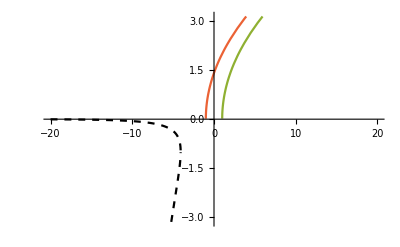

```mathematica
{sol1,sol2} = Eigenvalues[T2.T1]/.{q-> Sqrt[2m (ϵ-v1)], qb-> Sqrt[2m (ϵ-v2)]};

nsub = {m->1,v1->1,v2->-1,a->1};

Plot[Evaluate[{sol1, sol2,Sqrt[2m (ϵ-v1)], Sqrt[2m (ϵ-v2)]}/.nsub],{ϵ,-20,20},PlotRange->{-π,π},PlotStyle->{{Black,Dashed},{Black,Dashed},Automatic,Automatic}]
```

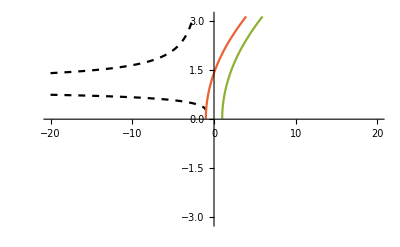

```mathematica
{sol1,sol2} = Eigenvalues[T2]/.{q-> Sqrt[2m (ϵ-v1)], qb-> Sqrt[2m (ϵ-v2)]};

nsub = {m->1,v1->1,v2->-1,a->1};

k = 1/(2a)Arg[sol];
Plot[Evaluate[{sol1, sol2,Sqrt[2m (ϵ-v1)], Sqrt[2m (ϵ-v2)]}/.nsub],{ϵ,-20,20},PlotRange->{-π,π},PlotStyle->{{Black,Dashed},{Black,Dashed},Automatic,Automatic}]
```

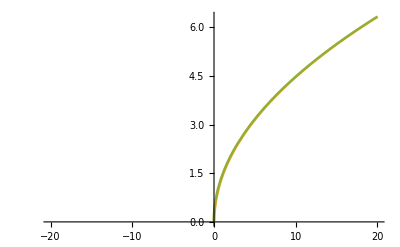

```mathematica
sol = %218/.{q-> Sqrt[2m (ϵ-v1)], qb-> Sqrt[2m (ϵ-v2)]};
nsub = {m->1,v1->0.05,v2->-0.05,a->1};

k = 1/(2a)Arg[sol];
Plot[Evaluate[{sol, Sqrt[2m (ϵ-v1)], Sqrt[2m (ϵ-v2)]}/.nsub],{ϵ,-20,20}]
```

```mathematica
Eigenvalues[ Sum[x[i] PauliMatrix[i],{i,0,3}]]
```

{x(0)-√((x(1))^2+(x(2))^2+(x(3))^2),x(0)+√((x(1))^2+(x(2))^2+(x(3))^2)}

```mathematica
{A1,A2}/.({ϕ2[0]==ϕ3[0],  ϕ2'[0]==ϕ3'[0]}//Solve[#,{A1,A2}]&)
```

(-(-B1b q-B2b q-B1b qb+B2b qb)/(2 q) | -(-B1b q-B2b q+B1b qb-B2b qb)/(2 q))

```mathematica
Table[D[{A1,A2}/.(Solve[eqs,{A1,A2}][[1]]),{coeff}],{coeff,{B1b,B2b}}]
```

(-(-q-qb)/(2 q) | -(qb-q)/(2 q)
-(qb-q)/(2 q) | -(-q-qb)/(2 q))

```mathematica
eqs = {ϕ2[0]==ϕ3[0],  ϕ2'[0]==ϕ3'[0]}
```

{A1+A2==B1b+B2b,ⅈ A1 q-ⅈ A2 q==ⅈ B1b qb-ⅈ B2b qb}